# Test of the modules in SimPack.m with a single s-band

## Goal

The modules in SimPack.m, used for the connection to FORTRAN , are presented in action here.

The example is a single s-band in fcc structure.

All data files  for the FORTRAN calculation are given in the directory.

```mathematica
dir=NotebookDirectory[];SetDirectory[dir];
```

## Init

The initialization of the group theory package is the first step.

```mathematica
Needs["GroupTheory`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Hamiltonian and parameters

### Hamiltonian

This is an s-band Hamiltonian up to third neighbors in the simple cubic structures. By appropriate chosen parameters you can investigate sc-, fcc- and bcc-structure.

```mathematica
ham00={{"(ss0)"+4 (Cos[π η] Cos[π ξ]+Cos[π ζ] (Cos[π η]+Cos[π ξ])) Subscript["(ssσ)", 1]+2 (Cos[2 π ζ]+Cos[2 π η]+Cos[ 2π ξ]) Subscript["(ssσ)", 2] +8 (Cos[ π ζ]Cos[ π η]Cos[ π ξ]) Subscript["(ssσ)", 3] }};
```

### Export parameters

This is the simplest parameter set for the fcc-structure.

```mathematica
pset={{"(ss0)",0.0},{Subscript["(ssσ)", 1],1.0},{Subscript["(ssσ)", 2],0.0},{Subscript["(ssσ)", 3],0.0}};
```

Export the parameters for use in SimPack

```mathematica
dd=GTTbParmExport[pset,"fcc_s.parm","Test data"];
```

1 | 2 | 3 | 4
(ss0) | (ssσ)_1 | (ssσ)_2 | (ssσ)_3
0. | 1. | 0. | 0.

### Export noisy parameters

To  test the fitting procedures, we will export some TB band structures with exactly known parameters. To the parameters noise will be added. The noisy parameters are the starting approximation in the fit.

First some random numbers are generated.

```mathematica
rd=RandomReal[{-.2,.2},4]
```

{-0.147663,0.126014,0.0561203,0.0781579}

The random numbers in the interval [-.2,.2] used in the test are actually.

```mathematica
rd0={0.0536011,0.13151,0.194298,0.156594};
```

The noise is added to the parameters and the noisy parameters are exported.

```mathematica
{pn,parms}=Transpose[pset];dparmr={pn,parms+rd0}//Transpose
```

{{(ss0),0.0536011},{(ssσ)_1,1.13151},{(ssσ)_2,0.194298},{(ssσ)_3,0.156594}}

```mathematica
GTTbParmExport[dparmr,"fcc_sn.parm","Test noise (-0.2,0.2)",ham00];
```

1 | 2 | 3 | 4
(ss0) | (ssσ)_1 | (ssσ)_2 | (ssσ)_3
0.0536011 | 1.13151 | 0.194298 | 0.156594

### Export Hamiltonian

Hamiltonians can be constructed in GTPack and exported as a FORTRAN module. This module will be used in the FORTRAN calculations.

```mathematica
GTTbToFortran[ham00,pset,3,"fcc_s.f90",GOVerbose->True]
```

H(1,1) = P(1) + 4._8*(ckx*cky + (ckx + cky)*ckz)*P(2) + 2._8*(Cos(2._8*kx*Pi) + Cos(2._8*ky*Pi) + Cos(2._8*kz*Pi))*P(3) + 8._8*ckx*cky*ckz*P(4)

fcc_s.f90

## Export k-mesh

### Band structure

In the FORTRAN band structure calculation we can use the k-mesh from GTPack. The k-vectors along the lines are exported.

```mathematica
kp=GTBZPath["fcc"];
kpl=GTBZLines[kp,{5,5,5,5,5,5}];
GTBZTbPointMesh["kfcc.lin",kpl,13,5]
```

Use k-points in FORTRAN-ETBM calculation for Bands

Output in file    : kfcc.lin

Number of k-points: 25

kfcc.lin

### DOS calculation

Gaussian smearing is used in GTPack to calculate the DOS. The same method is used in the external FORTRAN program. The FORTRAN code offers also the tetrahedron method. It is possible to get better results with a smaller number of k-points with the tetrahedron method.

The external DOS calculation will be performed for the same k-mesh like the GTPack DOS calculation.  Thus, we export a k-mesh from GTPack to be used in the band structure calculation in SimPack.

```mathematica
kpts=GTBZPointMesh[15,1,"fcc"];
```

20096 k-points calculated

```mathematica
GTBZTbPointMesh["kfcc.dos",kpts,13,5,GOOutput->"DOS"]
```

Use k-points in FORTRAN-ETBM calculation for DOS

Output in file    : kfcc.dos

Number of k-points: 20096

kfcc.dos

## Prepare SimPack results

Use the makefile to generate the FORTRAN executables for this test calculations. You will get:

```mathematica
FileNames["*.x"]
```

{tb_bands_s.x,tb_dos_s.x}

The input files are:

```mathematica
FileNames["*.in"]
```

{bands_dos.in,bands.in,dos.in}

Perform the FORTRAN calculations and you will have:

```mathematica
FileNames[{"*.bnd","*.dos","*.prt","verbose.*"}]
```

{dos.prt,fcc.dos,fcc_dos.bnd,fcc_dos.prt,fcc_s.bnd,fcc_s.prt,kfcc.dos,verbose.bnd,verbose.dos}

## Band structure

### GTPack

Hamiltonian and parameters are given. Thus we can directly calculate the band structure.

```mathematica
phfcc1=ham00 /.GTTbParmToRule[pset]
```

{{0.+4. (Cos[π η] Cos[π ξ]+Cos[π ζ] (Cos[π η]+Cos[π ξ]))}}

#### Bands

Maximum Abscissa = 4.48735

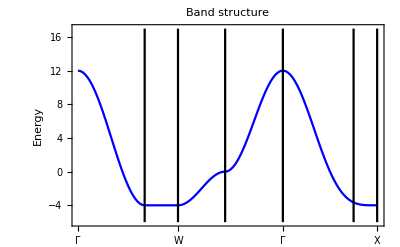

```mathematica
kp=GTBZPath["fcc"];
mfcc=GTBandStructure[phfcc1,kp,30,1,Joined->True,PlotRange->{{0,4.5},{-6.,17.}}]
```

#### Noisy bands

We will calculate the bands with the noisy parameters and compare this band structure with the exact one.

```mathematica
phfcc2=ham00 /.GTTbParmToRule[dparmr];
```

Maximum Abscissa = 4.48735

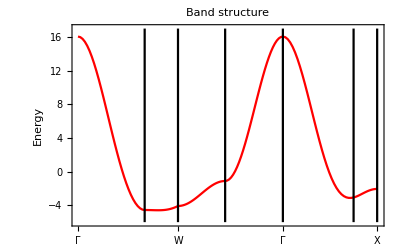

```mathematica
kp=GTBZPath["fcc"];
mfcc1=GTBandStructure[phfcc2,kp,30,1,Joined->True,PlotRange->{{0,4.5},{-6.,17.}},PlotStyle->Red]
```

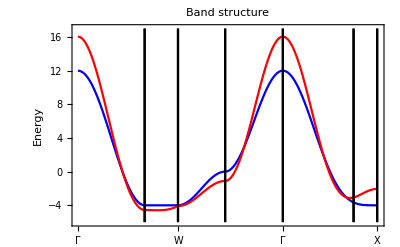

```mathematica
Show[mfcc,mfcc1]
```

The fit has to find from the noisy parameters the parameter set, which correspond to the exact band structure.

### Export bands for fit

The exact band structure from the figure above is exported to be used in the test of fitting procedures. From kpl we need only the pure k-points:

```mathematica
kpline=Transpose[kpl[[1]]][[3]];
```

```mathematica
bands1=GTBands[phfcc1,kpline,1,GOPlotBands->False,GOVerbose->True];
```

k-point | Eigenvalues
{0,0,0} |  12.0000
{0,0,1/4} |  9.6570
{0,0,1/2} |  4.0000
{0,0,3/4} | -1.6570
{0,0,1} | -4.0000
{0,1/8,1} | -4.0000
{0,1/4,1} | -4.0000
{0,3/8,1} | -4.0000
{0,1/2,1} | -4.0000
{1/8,1/2,7/8} | -3.4140
{1/4,1/2,3/4} | -2.0000
{3/8,1/2,5/8} | -0.5858
{1/2,1/2,1/2} |  0.0000
{3/8,3/8,3/8} |  1.7570
{1/4,1/4,1/4} |  6.0000
{1/8,1/8,1/8} |  10.2400
{0,0,0} |  12.0000
{3/16,3/16,0} |  9.4170
{3/8,3/8,0} |  3.6470
{9/16,9/16,0} | -1.4080
{3/4,3/4,0} | -3.6570
{13/16,13/16,0} | -3.8860
{7/8,7/8,0} | -3.9770
{15/16,15/16,0} | -3.9990
{1,1,0} | -4.0000

```mathematica
GTTbFitExport["energ_t.li",bands1]
```

number of k-points = 25

number of bands    = 1

energ_t.li

### Read a FORTRAN band structure

The file fcc.bnd was generated by the corresponding FORTRAN program and the exact tight-binding parameters. It will be read in and the band structure is plotted. We have to provide the k-vectors from the lines to guarantee that the data set for the plot can be completed correctly. This is necessary to add the  position and names of symmetry points.

```mathematica
bfcc=GTTbReadBands["fcc_s.bnd",kpl];
```

Number of k-points : 25

Maximum Abscissa = 4.48735

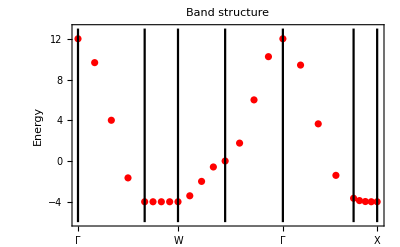

```mathematica
ffcc=GTBandsPlot[bfcc,1,PlotRange->{{0,4.5},{-6.,13.}},PlotStyle->{Red}]
```

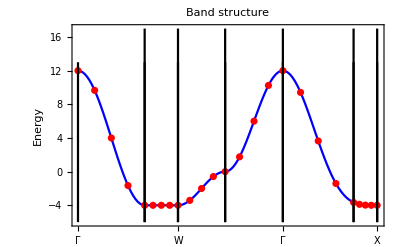

```mathematica
Show[mfcc,ffcc]
```

Of course the results agree.

## DOS

For calculations with dense k-meshes the DOS calculation in GTPack might be slow.  The possibility to do DOS calculations with an external FORTRAN program will accelerate the calculations.

### Calculation with GTPack

This is the DOS calculation for the band of the example with a really dense k-mesh.

20096 k-points calculated

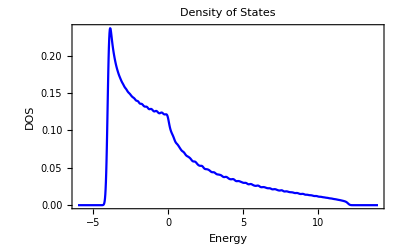

```mathematica
dosp={15,1,-6,14,1001,0.1,1};dfcc=GTDensityOfStates[phfcc1,"fcc",dosp]
```

fcc.dos contains the DOS calculated by means of SimPack. The file contains only DOS and IDOS.

```mathematica
<<sim_test.m
```

```mathematica
dinti
```

```mathematica
{fdos,fidos}=GTTbReadDOS1["fcc.dos",{},GOPlotDos->False];
```

emin | de  | emax |  Fermi energy E_F | electrons
-6. | 0.02 | 14. | 11.9966 | 1.

number of densities 2  energy points = 1000

| total
DOS | 0.00280227
N_el | 0.999688

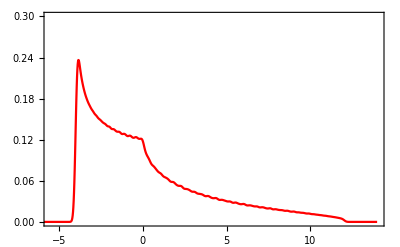

```mathematica
pll=ListPlot[fdos,Joined->True,PlotStyle->Red,Frame->True,PlotRange->{{-5.5,14},{0,0.3}}]
```

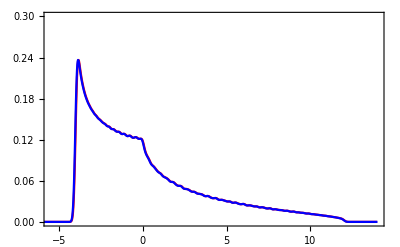

```mathematica
Show[pll,dfcc]
```

Of course the results agree exactly. We can also plot DOS and IDOS  together. Due to the order of magnitude it is not a very nice plot!

emin | de  | emax |  Fermi energy E_F | electrons
-6. | 0.02 | 14. | 11.9966 | 1.

number of densities 2  energy points = 1000

| total
DOS | 0.00280227
N_el | 0.999688

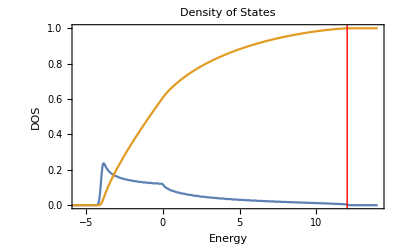

```mathematica
GTTbReadDOS1["fcc.dos",{},GOPlotDos->True,PlotRange->{{-5.5,14},{0,1}}]
```